# Rotating Neutron Star

## Quit Kernel before executing another top level section!

## Rotating NS, Default Polar Spherical

The metric as solved for by the RNSID code is of the form :
ds^2=- ⅇ^(γ+ρ)dt^2 + ⅇ^(γ-ρ)r^2 Sin[θ]^2(dϕ -ω dt)^2 + ⅇ^(2α)(dr^2+r^2 dθ^2)

```mathematica
lineElement[r_,θ_,ϕ_,γ_,ρ_,α_,ω_]:=- ⅇ^(γ+ρ)dt^2 + ⅇ^(γ-ρ)r^2 Sin[θ]^2(dϕ -ω dt)^2 + ⅇ^(2α)(dr^2+r^2 dθ^2);
```

```mathematica
gij={ {ⅇ^(γ-ρ)ω^2 r^2 Sin[θ]^2- ⅇ^(γ+ρ),0,0,-ⅇ^(γ-ρ)ω r^2 Sin[θ]^2},
         {0, ⅇ^(2α),0,0},{0,0,ⅇ^(2α) r^2,0},
         { - ⅇ^(γ-ρ)ω r^2 Sin[θ]^2,0,0,ⅇ^(γ-ρ)r^2 Sin[θ]^2} };
ugij=Inverse[gij];
γij=gij⟦2;;4,2;;4⟧;
uγij=Inverse[γij];
```

Display metric and inverse in matrix form

```mathematica
MatrixForm[gij]
MatrixForm[ugij]
MatrixForm[γij]
MatrixForm[uγij]
```

(-ⅇ^(γ+ρ)+ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2 | 0 | 0 | -ⅇ^(γ-ρ) r^2 ω Sin[θ]^2
0 | ⅇ^(2 α) | 0 | 0
0 | 0 | ⅇ^(2 α) r^2 | 0
-ⅇ^(γ-ρ) r^2 ω Sin[θ]^2 | 0 | 0 | ⅇ^(γ-ρ) r^2 Sin[θ]^2)

(-ⅇ^(-γ-ρ) | 0 | 0 | -ⅇ^(-γ-ρ) ω
0 | ⅇ^(-2 α) | 0 | 0
0 | 0 | ⅇ^(-2 α)/r^2 | 0
-ⅇ^(-γ-ρ) ω | 0 | 0 | -(ⅇ^(-4 α-2 γ) Csc[θ]^2 (-ⅇ^(4 α+γ+ρ) r^2+ⅇ^(4 α+γ-ρ) r^4 ω^2 Sin[θ]^2))/r^4)

(ⅇ^(2 α) | 0 | 0
0 | ⅇ^(2 α) r^2 | 0
0 | 0 | ⅇ^(γ-ρ) r^2 Sin[θ]^2)

(ⅇ^(-2 α) | 0 | 0
0 | ⅇ^(-2 α)/r^2 | 0
0 | 0 | (ⅇ^(-γ+ρ) Csc[θ]^2)/r^2)

```mathematica
FullSimplify[Det[γij]]
```

ⅇ^(4 α+γ-ρ) r^4 Sin[θ]^2

The shift as 3 - vector chosen directly from the metric

```mathematica
beta3down={0,0,-ω ⅇ^(γ-ρ)r^2 Sin[θ]^2}
beta3up=FullSimplify[uγij.beta3down]
beta3mag = FullSimplify[ beta3down.uγij.beta3down ]
```

{0,0,-ⅇ^(γ-ρ) r^2 ω Sin[θ]^2}

{0,0,-ω}

ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2

The lapse given our choice of shift directly from the line element

```mathematica
lapse=Sqrt[ - gij⟦1,1⟧+ beta3mag ]
```

√(ⅇ^(γ+ρ))

The shift as 4 - vector

```mathematica
beta4down=Flatten[{beta3mag,beta3down}]
beta4up=FullSimplify[ugij.beta4down]
beta4mag = FullSimplify[ beta4up.beta4down ]
checkBetaMag= FullSimplify[beta4down.ugij.beta4down/beta3mag] (* Should be Unity! *)
```

{ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2,0,0,-ⅇ^(γ-ρ) r^2 ω Sin[θ]^2}

{0,0,0,-ω}

ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2

1

## Rotating NS, Isotropic Polar Spherical

The metric as solved for by the RNSID code is of the form ds^2:=(ⅇ^(γ-ρ)ω^2 r^2 Sin[θ]^2- ⅇ^(γ+ρ))dt^2 -2 ⅇ^(α+(γ-ρ)/2)ω r^2 Sin[θ]^2 dζ dt + ⅇ^(2α)(dr^2+r^2 dθ^2+r^2 Sin[θ]^2 dζ^2)

```mathematica
lineElement[r_,θ_,ϕ_,γ_,ρ_,α_,ω_]:=(ⅇ^(γ-ρ)ω^2 r^2 Sin[θ]^2- ⅇ^(γ+ρ))dt^2 -2 ⅇ^(α+(γ-ρ)/2)ω r^2 Sin[θ]^2 dζ dt + ⅇ^(2α)(dr^2+r^2 dθ^2+r^2 Sin[θ]^2 dζ^2);
```

```mathematica
gij={ {ⅇ^(γ-ρ)ω^2 r^2 Sin[θ]^2- ⅇ^(γ+ρ),0,0,-ⅇ^(α+(γ-ρ)/2)ω r^2 Sin[θ]^2},
         {0, ⅇ^(2α),0,0},{0,0,ⅇ^(2α) r^2,0},
         { - ⅇ^(α+(γ-ρ)/2)ω r^2 Sin[θ]^2,0,0,ⅇ^(2α)r^2 Sin[θ]^2} };
ugij=Inverse[gij];
γij=gij⟦2;;4,2;;4⟧;
uγij=Inverse[γij];
```

Display metric and inverse in matrix form

```mathematica
MatrixForm[gij]
MatrixForm[ugij]
MatrixForm[γij]
MatrixForm[uγij]
```

(-ⅇ^(γ+ρ)+ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2 | 0 | 0 | -ⅇ^(α+(γ-ρ)/2) r^2 ω Sin[θ]^2
0 | ⅇ^(2 α) | 0 | 0
0 | 0 | ⅇ^(2 α) r^2 | 0
-ⅇ^(α+(γ-ρ)/2) r^2 ω Sin[θ]^2 | 0 | 0 | ⅇ^(2 α) r^2 Sin[θ]^2)

(-ⅇ^(-γ-ρ) | 0 | 0 | -ⅇ^(-α-γ+(γ-ρ)/2-ρ) ω
0 | ⅇ^(-2 α) | 0 | 0
0 | 0 | ⅇ^(-2 α)/r^2 | 0
-ⅇ^(-α-γ+(γ-ρ)/2-ρ) ω | 0 | 0 | -(ⅇ^(-6 α-γ-ρ) Csc[θ]^2 (-ⅇ^(4 α+γ+ρ) r^2+ⅇ^(4 α+γ-ρ) r^4 ω^2 Sin[θ]^2))/r^4)

(ⅇ^(2 α) | 0 | 0
0 | ⅇ^(2 α) r^2 | 0
0 | 0 | ⅇ^(2 α) r^2 Sin[θ]^2)

(ⅇ^(-2 α) | 0 | 0
0 | ⅇ^(-2 α)/r^2 | 0
0 | 0 | (ⅇ^(-2 α) Csc[θ]^2)/r^2)

The shift as 3 - vector chosen directly from the metric

```mathematica
beta3down=gij⟦1,2;;4⟧
beta3up=FullSimplify[uγij.beta3down]
beta3mag = FullSimplify[ beta3down.uγij.beta3down ]
```

{0,0,-ⅇ^(α+(γ-ρ)/2) r^2 ω Sin[θ]^2}

{0,0,-ⅇ^(1/2 (-2 α+γ-ρ)) ω}

ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2

The lapse given our choice of shift directly from the line element

```mathematica
lapse=Sqrt[ - gij⟦1,1⟧+ beta3mag ]
```

√(ⅇ^(γ+ρ))

```mathematica
Simplify [ beta3down⟦3⟧ (uγij⟦3,3⟧-ugij⟦4,4⟧ )/ugij⟦1,4⟧ ]
```

ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2

The shift as 4 - vector

```mathematica
beta4down=Flatten[{beta3mag,beta3down}]
beta4up=FullSimplify[ugij.beta4down]
beta4mag = FullSimplify[ beta4up.beta4down ]
checkBetaMag= FullSimplify[beta4down.ugij.beta4down/beta3mag] (* Should be Unity! *)
```

{ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2,0,0,-ⅇ^(α+(γ-ρ)/2) r^2 ω Sin[θ]^2}

{0,0,0,-ⅇ^(1/2 (-2 α+γ-ρ)) ω}

ⅇ^(γ-ρ) r^2 ω^2 Sin[θ]^2

1

## Rotating NS, Default Polar Spherical to Cartesian

### Construct the line element

The metric as solved for by the RNSID code is of the form :
ds^2=- ⅇ^(γ+ρ)dt^2 + ⅇ^(γ-ρ)r^2 Sin[θ]^2(dϕ -ω dt)^2 + ⅇ^(2α)(dr^2+r^2 dθ^2)

Converting to Cartesian base with the components still being governed by r,θ,ϕ .... 
   dr^2=( Cos[ϕ]Sin[θ]dx + Sin[ϕ]Sin[θ]dy+Cos[θ]dz)^2
   r^2 dθ^2=( Cos[ϕ] Cos[θ] dx + Sin[ϕ] Cos[θ] dy - Sin[θ] dz )^2
   r^2 Sin[θ]^2 dϕ^2=( Cos[ϕ] dy - Sin[ϕ] dx )^2 
   r^2 Sin[θ]^2 dϕ=x dy - y dx

```mathematica
lineElement[x_,y_,z_,γ_,ρ_,α_,ω_]:=-(ⅇ^(γ+ρ)-ω^2(x^2+y^2)ⅇ^(γ-ρ))dt^2  + 2ω ⅇ^(γ-ρ) ( y dx - x dy ) dt + ⅇ^(γ-ρ) (  x dy - y dx )^2/(x^2+y^2) + ⅇ^(2α)(  (x dx + y dy )^2/(x^2+y^2) + dz^2) ;
```

Verify the line element worked (somehow this isn' t obviously the case?)

```mathematica
lineElement[x,y,z,γ,ρ,α,ω]
```

(ⅇ^(γ-ρ) (dy x-dx y)^2)/(x^2+y^2)+ⅇ^(2 α) (dz^2+(dx x+dy y)^2/(x^2+y^2))+2 dt ⅇ^(γ-ρ) (-dy x+dx y) ω+dt^2 (-ⅇ^(γ+ρ)+ⅇ^(γ-ρ) (x^2+y^2) ω^2)

Get the metric components from the above element

```mathematica
dtdtcoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dt,0,2}], 2]
dxdxcoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dx,0,2}], 2]
dydycoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dy,0,2}], 2]
dzdzcoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dz,0,2}], 2]

dxdtcoeff=SeriesCoefficient[Series[ SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dx,0,1}], 1],{dt,0,1}],1]
dydtcoeff=SeriesCoefficient[Series[ SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dy,0,1}], 1],{dt,0,1}],1]

dxdycoeff=SeriesCoefficient[Series[ SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dx,0,1}], 1],{dy,0,1}],1]
```

-ⅇ^(γ-ρ) (ⅇ^(2 ρ)-x^2 ω^2-y^2 ω^2)

(ⅇ^-ρ (ⅇ^(2 α+ρ) x^2+ⅇ^γ y^2))/(x^2+y^2)

(ⅇ^-ρ (ⅇ^γ x^2+ⅇ^(2 α+ρ) y^2))/(x^2+y^2)

ⅇ^(2 α)

2 ⅇ^(γ-ρ) y ω

-2 ⅇ^(γ-ρ) x ω

(2 ⅇ^-ρ (-ⅇ^γ+ⅇ^(2 α+ρ)) x y)/(x^2+y^2)

### Set the spatial metric :

Use the above coefficients to construct the spatial metric

```mathematica
γij={{ dxdxcoeff,1/2 dxdycoeff,0},{1/2 dxdycoeff,dydycoeff,0},{0,0,dzdzcoeff}}
γij={{(ⅇ^(2 α) x^2+ⅇ^σ y^2)/(x^2+y^2),((-ⅇ^σ+ⅇ^(2 α)) x y)/(x^2+y^2),0},{((-ⅇ^σ+ⅇ^(2 α)) x y)/(x^2+y^2),(ⅇ^σ x^2+ⅇ^(2 α) y^2)/(x^2+y^2),0},{0,0,ⅇ^(2 α)}}
uγij=FullSimplify[Inverse[γij]];
MatrixForm[γij]
MatrixForm[uγij]
```

{{(ⅇ^-ρ (ⅇ^(2 α+ρ) x^2+ⅇ^γ y^2))/(x^2+y^2),(ⅇ^-ρ (-ⅇ^γ+ⅇ^(2 α+ρ)) x y)/(x^2+y^2),0},{(ⅇ^-ρ (-ⅇ^γ+ⅇ^(2 α+ρ)) x y)/(x^2+y^2),(ⅇ^-ρ (ⅇ^γ x^2+ⅇ^(2 α+ρ) y^2))/(x^2+y^2),0},{0,0,ⅇ^(2 α)}}

{{(ⅇ^(2 α) x^2+ⅇ^σ y^2)/(x^2+y^2),((ⅇ^(2 α)-ⅇ^σ) x y)/(x^2+y^2),0},{((ⅇ^(2 α)-ⅇ^σ) x y)/(x^2+y^2),(ⅇ^σ x^2+ⅇ^(2 α) y^2)/(x^2+y^2),0},{0,0,ⅇ^(2 α)}}

((ⅇ^(2 α) x^2+ⅇ^σ y^2)/(x^2+y^2) | ((ⅇ^(2 α)-ⅇ^σ) x y)/(x^2+y^2) | 0
((ⅇ^(2 α)-ⅇ^σ) x y)/(x^2+y^2) | (ⅇ^σ x^2+ⅇ^(2 α) y^2)/(x^2+y^2) | 0
0 | 0 | ⅇ^(2 α))

((ⅇ^(-2 α) x^2+ⅇ^-σ y^2)/(x^2+y^2) | (x y (ⅇ^(-2 α)-Cosh[σ]+Sinh[σ]))/(x^2+y^2) | 0
(x y (ⅇ^(-2 α)-Cosh[σ]+Sinh[σ]))/(x^2+y^2) | (ⅇ^-σ x^2+ⅇ^(-2 α) y^2)/(x^2+y^2) | 0
0 | 0 | ⅇ^(-2 α))

### Set the shift :

```mathematica
beta3down= 1/2{ dxdtcoeff, dydtcoeff, 0}
beta3down = {ⅇ^σ y ω,-ⅇ^σ x ω,0}
beta3up = Simplify[uγij.beta3down]



beta3mag=Simplify[beta3up.beta3down]
```

{ⅇ^(γ-ρ) y ω,-ⅇ^(γ-ρ) x ω,0}

{ⅇ^σ y ω,-ⅇ^σ x ω,0}

{y ω,-x ω,0}

ⅇ^σ (x^2+y^2) ω^2

### Set the lapse :

```mathematica
(*lapse=FullSimplify[ Sqrt[ - dtdtcoeff + beta3mag ]]*)
```

### Set the Full 4-metric

```mathematica
gij = { Flatten[{beta3mag-lapse^2,beta3down}],
           Flatten[ {beta3down⟦1⟧,γij⟦1,1;;3⟧}],
           Flatten[ {beta3down⟦2⟧,γij⟦2,1;;3⟧}],
           Flatten[ {beta3down⟦3⟧,γij⟦3,1;;3⟧}]};
ugij=Simplify[Inverse[gij]];
MatrixForm[gij]
MatrixForm[ugij]
```

(-lapse^2+ⅇ^σ (x^2+y^2) ω^2 | ⅇ^σ y ω | -ⅇ^σ x ω | 0
ⅇ^σ y ω | (ⅇ^(2 α) x^2+ⅇ^σ y^2)/(x^2+y^2) | ((ⅇ^(2 α)-ⅇ^σ) x y)/(x^2+y^2) | 0
-ⅇ^σ x ω | ((ⅇ^(2 α)-ⅇ^σ) x y)/(x^2+y^2) | (ⅇ^σ x^2+ⅇ^(2 α) y^2)/(x^2+y^2) | 0
0 | 0 | 0 | ⅇ^(2 α))

(-1/lapse^2 | (y ω)/lapse^2 | -(x ω)/lapse^2 | 0
(y ω)/lapse^2 | (ⅇ^(-2 α) lapse^2 x^2+ⅇ^-σ lapse^2 y^2-y^2 (x^2+y^2) ω^2)/(lapse^2 (x^2+y^2)) | (x y (ⅇ^(-2 α) lapse^2-ⅇ^-σ lapse^2+(x^2+y^2) ω^2))/(lapse^2 (x^2+y^2)) | 0
-(x ω)/lapse^2 | (x y (ⅇ^(-2 α) lapse^2-ⅇ^-σ lapse^2+(x^2+y^2) ω^2))/(lapse^2 (x^2+y^2)) | (ⅇ^-σ lapse^2 x^2+ⅇ^(-2 α) lapse^2 y^2-x^2 (x^2+y^2) ω^2)/(lapse^2 (x^2+y^2)) | 0
0 | 0 | 0 | ⅇ^(-2 α))

### Construct Rules and Lists to Convert to/from Functions

Create a spatial metric with Coordinate - dependent metric potentials, introducing the variable change σ = γ-ρ with additional introduction of functional dependence

```mathematica
coordvars={x,y,z};
sTof:={γ-ρ->σ[x,y,z],γ->γ[x,y,z] ,ρ->ρ[x,y,z], α->α[x,y,z], ω->ω[x,y,z], σ-> σ[x,y,z]};
γijc=γij/.sTof;
uγijc=FullSimplify[Inverse[γijc]];
beta3downc=beta3down/.sTof;
beta3upc = beta3up/.sTof;
lapsec = lapse/.sTof;
```

Introduce lists to go back to non - function versions of the metric potential as well as rules for making the results more readable

```mathematica
fTos:={γ[x,y,z]->γ,ρ[x,y,z]->ρ,α[x,y,z]->α,σ[x,y,z]->σ,ω[x,y,z]->ω};
readablederivs:=Flatten[ {
   {Derivative[0,1,0][α][x,y,z]-> dαdy,Derivative[1,0,0][α][x,y,z]-> dαdx,Derivative[0,0,1][α][x,y,z]-> dαdz},
{Derivative[0,1,0][ω][x,y,z]-> dωdy,Derivative[1,0,0][ω][x,y,z]-> dωdx,Derivative[0,0,1][ω][x,y,z]-> dωdz},
{Derivative[0,1,0][σ][x,y,z]-> dσdy,Derivative[1,0,0][σ][x,y,z]-> dσdx,Derivative[0,0,1][σ][x,y,z]-> dσdz},
{Derivative[0,1,0][ρ][x,y,z]-> dρdy,Derivative[1,0,0][ρ][x,y,z]-> dρdx,Derivative[0,0,1][ρ][x,y,z]-> dρdz},
{Derivative[0,1,0][γ][x,y,z]-> dγdy,Derivative[1,0,0][γ][x,y,z]-> dγdx,Derivative[0,0,1][γ][x,y,z]-> dγdz},
{Derivative[0,2,0][α][x,y,z]-> d2αdy,Derivative[2,0,0][α][x,y,z]-> d2αdx,Derivative[0,0,2][α][x,y,z]-> d2αdz},
{Derivative[0,2,0][ω][x,y,z]-> d2ωdy,Derivative[2,0,0][ω][x,y,z]-> d2ωdx,Derivative[0,0,2][ω][x,y,z]-> d2ωdz},
{Derivative[0,2,0][σ][x,y,z]-> d2σdy,Derivative[2,0,0][σ][x,y,z]-> d2σdx,Derivative[0,0,2][σ][x,y,z]-> d2σdz},
{Derivative[0,2,0][ρ][x,y,z]-> d2ρdy,Derivative[2,0,0][ρ][x,y,z]-> d2ρdx,Derivative[0,0,2][ρ][x,y,z]-> d2ρdz},
{Derivative[0,2,0][γ][x,y,z]-> d2γdy,Derivative[2,0,0][γ][x,y,z]-> d2γdx,Derivative[0,0,2][γ][x,y,z]-> d2γdz}}];
```

```mathematica
fullreadable:=Flatten[{fTos,readablederivs}];
```

```mathematica
dρdγ2dσ:={ dγdx-dρdx== dσdx,dγdy-dρdy==dσdy,dγdz-dρdz==dσdz,γ-ρ==σ};
```

### The Christoffels

Create a rule for constructing the 3 - Christoffels

```mathematica
gamma[i_,j_,k_] :=FullSimplify[ 1/2 Sum[  uγijc⟦ell⟧⟦i⟧ ( D[γijc⟦ell⟧⟦j⟧,coordvars⟦k⟧] +D[γijc⟦ell⟧⟦k⟧,coordvars⟦j⟧] -D[γijc⟦j⟧⟦k⟧,coordvars⟦ell⟧] )  ,{ell,1,3}]];
```

### Conformal Transformation

Conformal Transformation

```mathematica
χc=FullSimplify[(Det[γijc])^-3];
cγijc=FullSimplify[χc γijc];
ucγijc=FullSimplify[ Inverse[cγijc]];
confgamma[i_,j_,k_] :=FullSimplify[ 1/2 Sum[  ucγijc⟦ell⟧⟦i⟧ ( D[cγijc⟦ell⟧⟦j⟧,coordvars⟦k⟧] +D[cγijc⟦ell⟧⟦k⟧,coordvars⟦j⟧] -D[cγijc⟦j⟧⟦k⟧,coordvars⟦ell⟧] )  ,{ell,1,3}]];
```

```mathematica
χc
```

ⅇ^(-3 (4 α[x,y,z]+σ[x,y,z]))

### Check the Gauge

Check the lapse condition
  β^j∂_j α = 2 α K

```mathematica
advectα = FullSimplify[ Sum[beta3upc⟦j⟧ D[lapsec,coordvars⟦j⟧] ,{j,1,3}],dρdγ2dσ];
advectα/.{fullreadable}
```

{0}

Set the auxiliary variable for the shift condition, assuming stationarity:
  3/4 B^i=-β^j∂_j β^i

```mathematica
Bi=FullSimplify[Table[ -4/3 Sum[beta3upc⟦j⟧ D[ beta3upc⟦i⟧,coordvars⟦j⟧],{j,1,3}],{i,1,3}]];
Bi/.{fullreadable}
```

{{4/3 ω (y (dωdy x-dωdx y)+x ω),4/3 ω (x (-dωdy x+dωdx y)+y ω),0}}

Check whether the 2^nd condition is satisfied:
   -β^j ∂_j B^i =β^j∂_j (Γ̃)^i-η B^i
   or
    η B^i=β^j∂_j Γ^i+β^j ∂_j B^i=β^j∂_j ((Γ̃)^i+B^i)
   where (Γ̃)^i= (γ̃)^jk((Γ̃)^i)_jk

```mathematica
auxGamma=FullSimplify[ Table[ Sum[ ucγijc⟦j⟧⟦k⟧ confgamma[i,j,k],{j,1,3},{k,1,3}] ,{i,1,3}]];
auxGamma/.{fullreadable}
```

{{(ⅇ^(2 (5 α+σ)) (ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))))/(x^2+y^2),(ⅇ^(2 (5 α+σ)) (ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))))/(x^2+y^2),(6 dαdz+dσdz) ⅇ^(10 α+3 σ)}}

```mathematica
(auxGamma⟦1⟧+Bi⟦1⟧)/.{fullreadable}
```

{(ⅇ^(2 (5 α+σ)) (ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))))/(x^2+y^2)+4/3 ω (y (dωdy x-dωdx y)+x ω)}

```mathematica
shiftCheck = Table[ Sum[beta3upc⟦j⟧ D[auxGamma⟦i⟧+Bi⟦i⟧,coordvars⟦j⟧],{j,1,3}],{i,1,3}];
Simplify[shiftCheck]/.{fullreadable}
```

{{y ω (-(2 ⅇ^(2 (5 α+σ)) x (ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))))/((x^2+y^2)^2)+(2 (5 dαdx+dσdx) ⅇ^(2 (5 α+σ)) (ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))))/(x^2+y^2)+4/3 dωdx (y (dωdy x-dωdx y)+x ω)+1/(x^2+y^2)ⅇ^(2 (5 α+σ)) (ⅇ^σ (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+dσdx ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+2 dαdx ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))+ⅇ^σ x (6 dαdx+dσdx+6 d2αdx x+d2σdx x+6 y α^(1,1,0)[x,y,z]+y σ^(1,1,0)[x,y,z])+ⅇ^(2 α) (1+2 y (-2 dαdy-dσdy+(2 d2αdx+d2σdx) y-x (2 α^(1,1,0)[x,y,z]+σ^(1,1,0)[x,y,z]))))+4/3 ω (dωdx x+ω+y (dωdy-d2ωdx y+x ω^(1,1,0)[x,y,z])))-x ω (-(2 ⅇ^(2 (5 α+σ)) y (ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))))/((x^2+y^2)^2)+(2 (5 dαdy+dσdy) ⅇ^(2 (5 α+σ)) (ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))))/(x^2+y^2)+4/3 dωdy (y (dωdy x-dωdx y)+x ω)+1/(x^2+y^2)ⅇ^(2 (5 α+σ)) (dσdy ⅇ^σ x (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+2 dαdy ⅇ^(2 α) (x+2 y (-(2 dαdy+dσdy) x+(2 dαdx+dσdx) y))+ⅇ^σ x (6 dαdy+dσdy+6 d2αdy y+d2σdy y+6 x α^(1,1,0)[x,y,z]+x σ^(1,1,0)[x,y,z])-2 ⅇ^(2 α) (2 dαdy x+dσdy x-y (4 dαdx+2 dσdx-2 d2αdy x-d2σdy x+2 y α^(1,1,0)[x,y,z]+y σ^(1,1,0)[x,y,z])))+4/3 ω (2 dωdy x+y (-2 dωdx+d2ωdy x-y ω^(1,1,0)[x,y,z]))),y ω (-(2 ⅇ^(2 (5 α+σ)) x (ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))))/((x^2+y^2)^2)+(2 (5 dαdx+dσdx) ⅇ^(2 (5 α+σ)) (ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))))/(x^2+y^2)+4/3 dωdx (x (-dωdy x+dωdx y)+y ω)+1/(x^2+y^2)ⅇ^(2 (5 α+σ)) (dσdx ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+2 dαdx ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))+2 ⅇ^(2 α) (4 dαdy x+2 dσdy x-2 dαdx y-dσdx y-2 d2αdx x y-d2σdx x y+2 x^2 α^(1,1,0)[x,y,z]+x^2 σ^(1,1,0)[x,y,z])+ⅇ^σ y (6 dαdx+dσdx+6 d2αdx x+d2σdx x+6 y α^(1,1,0)[x,y,z]+y σ^(1,1,0)[x,y,z]))-4/3 ω (2 dωdy x-2 dωdx y+x (-d2ωdx y+x ω^(1,1,0)[x,y,z])))-x ω (-(2 ⅇ^(2 (5 α+σ)) y (ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))))/((x^2+y^2)^2)+(2 (5 dαdy+dσdy) ⅇ^(2 (5 α+σ)) (ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))))/(x^2+y^2)+4/3 dωdy (x (-dωdy x+dωdx y)+y ω)+1/(x^2+y^2)ⅇ^(2 (5 α+σ)) (ⅇ^σ (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+dσdy ⅇ^σ y (-1+6 dαdx x+dσdx x+6 dαdy y+dσdy y)+2 dαdy ⅇ^(2 α) (y+2 x (2 dαdy x+dσdy x-(2 dαdx+dσdx) y))+ⅇ^σ y (6 dαdy+dσdy+6 d2αdy y+d2σdy y+6 x α^(1,1,0)[x,y,z]+x σ^(1,1,0)[x,y,z])+ⅇ^(2 α) (1+2 x (-2 dαdx-dσdx+2 d2αdy x+d2σdy x-y (2 α^(1,1,0)[x,y,z]+σ^(1,1,0)[x,y,z]))))+4/3 ω (dωdy y+ω+x (dωdx-d2ωdy x+y ω^(1,1,0)[x,y,z]))),ⅇ^(10 α+3 σ) ω (-x ((10 dαdy+3 dσdy) (6 dαdz+dσdz)+6 α^(0,1,1)[x,y,z]+σ^(0,1,1)[x,y,z])+y ((10 dαdx+3 dσdx) (6 dαdz+dσdz)+6 α^(1,0,1)[x,y,z]+σ^(1,0,1)[x,y,z]))}}

### Set the Extrinsic Curvature without Christoffels, beta raised:

The Extrinsic Curvature here is constructed as (Alcubierre Eq. 2.3.12)
K_ij=1/(2α)( D_i β_j+ D_j β_i) =1/(2α)( D_i(γ_jk β^k)+ D_j(γ_ik β^k))
        = 1/(2α)( γ_jk∂_i β^k+ γ_ik∂_j β^k+β^k∂_k g_ij )

Contract the shift with the spatial Christoffels, betaGam=β_k Γ_ij^k

```mathematica
αKXX=FullSimplify[  Sum[ γijc⟦1,k⟧ D[beta3upc⟦k⟧,coordvars⟦1⟧] + γijc⟦1,k⟧  D[beta3upc⟦k⟧,coordvars⟦1⟧]+beta3upc⟦k⟧ D[ γijc⟦1,1⟧,coordvars⟦k⟧] ,{k,1,3}]]/2;
αKYY=FullSimplify[ Sum[ γijc⟦2,k⟧ D[beta3upc⟦k⟧,coordvars⟦2⟧] + γijc⟦2,k⟧  D[beta3upc⟦k⟧,coordvars⟦2⟧]+beta3upc⟦k⟧ D[ γijc⟦2,2⟧,coordvars⟦k⟧] ,{k,1,3}]]/2;
αKZZ=FullSimplify[ Sum[ γijc⟦3,k⟧ D[beta3upc⟦k⟧,coordvars⟦3⟧] + γijc⟦3,k⟧  D[beta3upc⟦k⟧,coordvars⟦3⟧]+beta3upc⟦k⟧ D[ γijc⟦3,3⟧,coordvars⟦k⟧],{k,1,3}]]/2;
αKXY=FullSimplify[Sum[ γijc⟦1,k⟧ D[beta3upc⟦k⟧,coordvars⟦2⟧] + γijc⟦2,k⟧  D[beta3upc⟦k⟧,coordvars⟦1⟧]+beta3upc⟦k⟧ D[ γijc⟦1,2⟧,coordvars⟦k⟧] ,{k,1,3}]]/2;
αKXZ=FullSimplify[ Sum[ γijc⟦1,k⟧ D[beta3upc⟦k⟧,coordvars⟦3⟧] + γijc⟦3,k⟧  D[beta3upc⟦k⟧,coordvars⟦1⟧]+beta3upc⟦k⟧ D[ γijc⟦1,3⟧,coordvars⟦k⟧],{k,1,3}]]/2;
αKYZ=FullSimplify[ Sum[ γijc⟦2,k⟧ D[beta3upc⟦k⟧,coordvars⟦3⟧] + γijc⟦3,k⟧  D[beta3upc⟦k⟧,coordvars⟦2⟧]+beta3upc⟦k⟧ D[ γijc⟦2,3⟧,coordvars⟦k⟧],{k,1,3}]]/2;
```

```mathematica
Kij = invα { {αKXX, αKXY, αKXZ },{αKXY, αKYY, αKYZ}, {αKXZ, αKYZ, αKZZ}}/.fullreadable
```

{{(invα (-2 ⅇ^(2 α) x^2 (dαdy x-dαdx y) ω+ⅇ^σ y (2 dωdx (x^2+y^2)+y (-dσdy x+dσdx y) ω)))/(2 (x^2+y^2)),(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2)),1/2 dωdz ⅇ^σ invα y},{(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2)),(invα (2 ⅇ^(2 α) y^2 (-dαdy x+dαdx y) ω-ⅇ^σ x (2 dωdy (x^2+y^2)+x (dσdy x-dσdx y) ω)))/(2 (x^2+y^2)),-1/2 dωdz ⅇ^σ invα x},{1/2 dωdz ⅇ^σ invα y,-1/2 dωdz ⅇ^σ invα x,-ⅇ^(2 α) invα (dαdy x-dαdx y) ω}}

Display resulting extrinsic curvature, with only minor simplifying still to do

```mathematica
readKij=FullSimplify[ Kij,dρdγ2dσ];
readK = FullSimplify[ Sum[uγij⟦i,j⟧readKij⟦i,j⟧,{i,1,3},{j,1,3}]];
```

```mathematica
listKijA := Table[  {ToString[K[coordvars⟦i⟧,coordvars⟦j⟧]], readKij⟦i,j⟧},{i,1,3},{j,i,3}];
TableForm[ Flatten[{listKijA,{"2αK",2 readK / invα},{"β^j∂_j α",advectα/.{fullreadable}}}],TableSpacing->{4,4}]
```

K[x, x]
(invα (-2 ⅇ^(2 α) x^2 (dαdy x-dαdx y) ω+ⅇ^σ y (2 dωdx (x^2+y^2)+y (-dσdy x+dσdx y) ω)))/(2 (x^2+y^2))
K[x, y]
(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2))
K[x, z]
1/2 dωdz ⅇ^σ invα y
K[y, y]
(invα (2 ⅇ^(2 α) y^2 (-dαdy x+dαdx y) ω-ⅇ^σ x (2 dωdy (x^2+y^2)+x (dσdy x-dσdx y) ω)))/(2 (x^2+y^2))
K[y, z]
-1/2 dωdz ⅇ^σ invα x
K[z, z]
-ⅇ^(2 α) invα (dαdy x-dαdx y) ω
2αK
-2 dωdy x+2 dωdx y+(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω
β^j∂_j α
0

### Set the Extrinsic Curvature without Christoffels, beta kept low:

The Extrinsic Curvature here is constructed as (Alcubierre Eq. 2.3.12)
K_ij=1/(2α)( ∂_i β_j+ ∂_j β_i-2 β_k Γ_ij^k) 
        = 1/(2α)( ∂_i β_j+ ∂_j β_i-β^k(∂_j g_ik+ ∂_i g_kj-∂_k g_ij) )

Contract the shift with the spatial Christoffels, betaGam=β_k Γ_ij^k

```mathematica
αKXX=FullSimplify[ D[beta3downc⟦1⟧,coordvars⟦1⟧] + D[beta3downc⟦1⟧,coordvars⟦1⟧] - Sum[ beta3upc⟦k⟧ ( D[ γijc⟦1,k⟧,coordvars⟦1⟧] + D[ γijc⟦k,1⟧,coordvars⟦1⟧] - D[ γijc⟦1,1⟧,coordvars⟦k⟧]) ,{k,1,3}]]/2;
αKYY=FullSimplify[ D[beta3downc⟦2⟧,coordvars⟦2⟧] + D[beta3downc⟦2⟧,coordvars⟦2⟧] - Sum[ beta3upc⟦k⟧ ( D[ γijc⟦2,k⟧,coordvars⟦2⟧] + D[ γijc⟦k,2⟧,coordvars⟦2⟧] - D[ γijc⟦2,2⟧,coordvars⟦k⟧]) ,{k,1,3}]]/2;
αKZZ=FullSimplify[ D[beta3downc⟦3⟧,coordvars⟦3⟧] + D[beta3downc⟦3⟧,coordvars⟦3⟧] - Sum[ beta3upc⟦k⟧ ( D[ γijc⟦3,k⟧,coordvars⟦3⟧] + D[ γijc⟦k,3⟧,coordvars⟦3⟧] - D[ γijc⟦3,3⟧,coordvars⟦k⟧]) ,{k,1,3}]]/2;
αKXY=FullSimplify[ D[beta3downc⟦1⟧,coordvars⟦2⟧] + D[beta3downc⟦2⟧,coordvars⟦1⟧] - Sum[ beta3upc⟦k⟧ ( D[ γijc⟦2,k⟧,coordvars⟦1⟧] + D[ γijc⟦k,1⟧,coordvars⟦2⟧] - D[ γijc⟦2,1⟧,coordvars⟦k⟧]) ,{k,1,3}]]/2;
αKXZ=FullSimplify[ D[beta3downc⟦3⟧,coordvars⟦1⟧] + D[beta3downc⟦1⟧,coordvars⟦3⟧] - Sum[ beta3upc⟦k⟧ ( D[ γijc⟦1,k⟧,coordvars⟦3⟧] + D[ γijc⟦k,3⟧,coordvars⟦1⟧] - D[ γijc⟦3,1⟧,coordvars⟦k⟧]) ,{k,1,3}]]/2;
αKYZ=FullSimplify[ D[beta3downc⟦2⟧,coordvars⟦3⟧] + D[beta3downc⟦3⟧,coordvars⟦2⟧] - Sum[ beta3upc⟦k⟧ ( D[ γijc⟦2,k⟧,coordvars⟦3⟧] + D[ γijc⟦k,3⟧,coordvars⟦2⟧] - D[ γijc⟦3,2⟧,coordvars⟦k⟧]) ,{k,1,3}]]/2;
```

```mathematica
Kij = invα { {αKXX, αKXY, αKXZ },{αKXY, αKYY, αKYZ}, {αKXZ, αKYZ, αKZZ}}/.fullreadable
```

{{(invα (-2 ⅇ^(2 α) x^2 (dαdy x-dαdx y) ω+ⅇ^σ y (2 dωdx (x^2+y^2)+y (-dσdy x+dσdx y) ω)))/(2 (x^2+y^2)),(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2)),1/2 dωdz ⅇ^σ invα y},{(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2)),(invα (2 ⅇ^(2 α) y^2 (-dαdy x+dαdx y) ω-ⅇ^σ x (2 dωdy (x^2+y^2)+x (dσdy x-dσdx y) ω)))/(2 (x^2+y^2)),-1/2 dωdz ⅇ^σ invα x},{1/2 dωdz ⅇ^σ invα y,-1/2 dωdz ⅇ^σ invα x,-ⅇ^(2 α) invα (dαdy x-dαdx y) ω}}

Display resulting extrinsic curvature, with only minor simplifying still to do

```mathematica
readKij=FullSimplify[ Kij,dρdγ2dσ];
readK = FullSimplify[ Sum[uγij⟦i,j⟧readKij⟦i,j⟧,{i,1,3},{j,1,3}]];
```

```mathematica
listKijB := Table[  {ToString[K[coordvars⟦i⟧,coordvars⟦j⟧]], readKij⟦i,j⟧},{i,1,3},{j,i,3}];
TableForm[ Flatten[{listKijB,{"2αK",2 readK / invα},{"β^j∂_j α",advectα/.{fullreadable}}}],TableSpacing->{4,4}]
```

K[x, x]
(invα (-2 ⅇ^(2 α) x^2 (dαdy x-dαdx y) ω+ⅇ^σ y (2 dωdx (x^2+y^2)+y (-dσdy x+dσdx y) ω)))/(2 (x^2+y^2))
K[x, y]
(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2))
K[x, z]
1/2 dωdz ⅇ^σ invα y
K[y, y]
(invα (2 ⅇ^(2 α) y^2 (-dαdy x+dαdx y) ω-ⅇ^σ x (2 dωdy (x^2+y^2)+x (dσdy x-dσdx y) ω)))/(2 (x^2+y^2))
K[y, z]
-1/2 dωdz ⅇ^σ invα x
K[z, z]
-ⅇ^(2 α) invα (dαdy x-dαdx y) ω
2αK
-2 dωdy x+2 dωdx y+(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω
β^j∂_j α
0

### Set the Extrinsic Curvature via the Christoffels:

The Extrinsic Curvature here is constructed as (Alcubierre Eq. 2.3.12)
K_ij=1/(2α)( ∂_i β_j+ ∂_j β_i-2 β_k Γ_ij^k) =1/α( ∂_((i) β_(j))-β_k Γ_ij^k)

Contract the shift with the spatial Christoffels, betaGam=β_k Γ_ij^k

```mathematica
betaGamXX=FullSimplify[beta3downc⟦1⟧*gamma[1,1,1]+beta3downc⟦2⟧*gamma[2,1,1]];
betaGamYY=FullSimplify[beta3downc⟦1⟧*gamma[1,2,2]+beta3downc⟦2⟧*gamma[2,2,2]];
betaGamZZ=FullSimplify[beta3downc⟦1⟧*gamma[1,3,3]+beta3downc⟦2⟧*gamma[2,3,3]];
betaGamXY=FullSimplify[beta3downc⟦1⟧*gamma[1,1,2]+beta3downc⟦2⟧*gamma[2,1,2]];
betaGamXZ=FullSimplify[beta3downc⟦1⟧*gamma[1,1,3]+beta3downc⟦2⟧*gamma[2,1,3]];
betaGamYZ=FullSimplify[beta3downc⟦1⟧*gamma[1,2,3]+beta3downc⟦2⟧*gamma[2,2,3]];
```

Matrix Forms of this and the symmetrized derivatives of the covariant shift, ∂_((i) β_(j))

```mathematica
betaGamij=Table[ 
FullSimplify[Sum[ beta3downc⟦k⟧ * gamma[k,i,j],{k,1,3}]],
{i,3},{j,3}];
symdBetaij=Table[
1/2 FullSimplify[ D[beta3downc⟦i⟧,coordvars⟦j⟧]+D[beta3downc⟦j⟧,coordvars⟦i⟧]],
{i,3},{j,3}];
```

```mathematica
Kij = invα FullSimplify[ symdBetaij - betaGamij ]/.fullreadable
```

{{(invα (-2 ⅇ^(2 α) x^2 (dαdy x-dαdx y) ω+ⅇ^σ y (2 dωdx (x^2+y^2)+y (-dσdy x+dσdx y) ω)))/(2 (x^2+y^2)),(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2)),1/2 dωdz ⅇ^σ invα y},{(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2)),(invα (2 ⅇ^(2 α) y^2 (-dαdy x+dαdx y) ω-ⅇ^σ x (2 dωdy (x^2+y^2)+x (dσdy x-dσdx y) ω)))/(2 (x^2+y^2)),-1/2 dωdz ⅇ^σ invα x},{1/2 dωdz ⅇ^σ invα y,-1/2 dωdz ⅇ^σ invα x,-ⅇ^(2 α) invα (dαdy x-dαdx y) ω}}

Display resulting extrinsic curvature, with only minor simplifying still to do

```mathematica
readKij=FullSimplify[ Kij,dρdγ2dσ];
readK = FullSimplify[ Sum[uγij⟦i,j⟧readKij⟦i,j⟧,{i,1,3},{j,1,3}]];
```

```mathematica
listKijC:= Table[  {ToString[K[coordvars⟦i⟧,coordvars⟦j⟧]], readKij⟦i,j⟧},{i,1,3},{j,i,3}];
TableForm[ Flatten[{listKijC,{"2αK",2 readK / invα},{"β^j∂_j α",advectα/.{fullreadable}}}],TableSpacing->{4,4}]
```

K[x, x]
(invα (-2 ⅇ^(2 α) x^2 (dαdy x-dαdx y) ω+ⅇ^σ y (2 dωdx (x^2+y^2)+y (-dσdy x+dσdx y) ω)))/(2 (x^2+y^2))
K[x, y]
(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2))
K[x, z]
1/2 dωdz ⅇ^σ invα y
K[y, y]
(invα (2 ⅇ^(2 α) y^2 (-dαdy x+dαdx y) ω-ⅇ^σ x (2 dωdy (x^2+y^2)+x (dσdy x-dσdx y) ω)))/(2 (x^2+y^2))
K[y, z]
-1/2 dωdz ⅇ^σ invα x
K[z, z]
-ⅇ^(2 α) invα (dαdy x-dαdx y) ω
2αK
-2 dωdy x+2 dωdx y+(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω
β^j∂_j α
0

### Compare Kijs

```mathematica
Simplify[ D[ r/(r+R),r]]
```

R/(r+R)^2

```mathematica
u
```

```mathematica
Simplify[2 γijc⟦1,1⟧ D[beta3upc⟦1⟧,coordvars⟦1⟧] + 2 γijc⟦1,2⟧ D[beta3upc⟦2⟧,coordvars⟦1⟧] + beta3upc⟦1⟧ D[γijc⟦1,1⟧,coordvars⟦1⟧] + beta3upc⟦2⟧ D[γijc⟦1,1⟧,coordvars⟦2⟧],dρdγ2dσ] /.fullreadable
```

(2 dωdx ⅇ^σ y (x^2+y^2)+(-2 dαdy ⅇ^(2 α) x^3+y (2 dαdx ⅇ^(2 α) x^2-dσdy ⅇ^σ x y+dσdx ⅇ^σ y^2)) ω)/(x^2+y^2)

```mathematica
listKijA⟦1,2⟧/.{ⅇ^α-> 0}
listKijB⟦1,2⟧
listKijC⟦1,2⟧
```

{K[x, y],(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2))}

{K[x, y],(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2))}

{K[x, y],(invα (-ⅇ^σ (dωdx x-dωdy y) (x^2+y^2)+x y (-2 ⅇ^(2 α) (dαdy x-dαdx y)+ⅇ^σ (dσdy x-dσdx y)) ω))/(2 (x^2+y^2))}

## Rotating NS, Isotropic Polar Spherical to Cartesian

The metric as solved for by the RNSID code is of the form :
ds^2=- ⅇ^(γ+ρ)dt^2 + ⅇ^(γ-ρ)r^2 Sin[θ]^2(dϕ -ω dt)^2 + ⅇ^(2α)(dr^2+r^2 dθ^2)
and then transform the coordinates (r̄,θ̄,ζ) such that r̄=r, θ̄=θ, ζ=ⅇ^((γ-ρ)/2-α)ϕ.
ds^2:=(ⅇ^(γ-ρ)ω^2 r^2 Sin[θ]^2- ⅇ^(γ+ρ))dt^2 -2 ⅇ^(α+(γ-ρ)/2)ω r^2 Sin[θ]^2 dζ dt + ⅇ^(2α)(dr^2+r^2 dθ^2+r^2 Sin[θ]^2 dζ^2)

Converting to Cartesian base with the components still being governed by (r,θ,ζ) ...
   dr^2=( Cos[ζ]Sin[θ]dx + Sin[ζ]Sin[θ]dy+Cos[θ]dz)^2
   r^2 dθ^2=( Cos[ζ] Cos[θ] dx + Sin[ζ] Cos[θ] dy - Sin[θ] dz )^2
   r^2 Sin[θ]^2 dζ^2=( Cos[ζ] dy - Sin[ζ] dx )^2 
   r^2 Sin[θ]^2 dζ=x dy - y dx

### Construct the line element and coefficients

```mathematica
lineElement[x_,y_,z_,γ_,ρ_,α_,ω_]:=-(ⅇ^(γ+ρ)-ω^2(x^2+y^2)ⅇ^(γ-ρ))dt^2  + 2ω ⅇ^(α+(γ-ρ)/2)( y dx - x dy ) dt + ⅇ^(2α)( dx^2+dy^2+dz^2) ;
```

Verify the line element worked (somehow this isn' t obviously the case?)

```mathematica
lineElement[x,y,z,γ,ρ,α,ω]
```

(dx^2+dy^2+dz^2) ⅇ^(2 α)+2 dt ⅇ^(α+(γ-ρ)/2) (-dy x+dx y) ω+dt^2 (-ⅇ^(γ+ρ)+ⅇ^(γ-ρ) (x^2+y^2) ω^2)

Get the metric components from the above element

```mathematica
dtdtcoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dt,0,2}], 2]
dxdxcoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dx,0,2}], 2]
dydycoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dy,0,2}], 2]
dzdzcoeff=SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dz,0,2}], 2]

dxdtcoeff=SeriesCoefficient[Series[ SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dx,0,1}], 1],{dt,0,1}],1]
dydtcoeff=SeriesCoefficient[Series[ SeriesCoefficient[ Series[ lineElement[x,y,z,γ,ρ,α,ω], {dy,0,1}], 1],{dt,0,1}],1]

dxdycoeff=0;
```

-ⅇ^(γ-ρ) (ⅇ^(2 ρ)-x^2 ω^2-y^2 ω^2)

ⅇ^(2 α)

ⅇ^(2 α)

ⅇ^(2 α)

2 ⅇ^(α+(γ-ρ)/2) y ω

-2 ⅇ^(α+(γ-ρ)/2) x ω

### Set the Analytic metric with gauge

#### Set the spatial metric :

Use the above coefficients to construct the spatial metric

```mathematica
γij={{ dxdxcoeff,1/2 dxdycoeff,0},{1/2 dxdycoeff,dydycoeff,0},{0,0,dzdzcoeff}}
uγij=FullSimplify[Inverse[γij]];
MatrixForm[γij]
MatrixForm[uγij]
```

{{ⅇ^(2 α),0,0},{0,ⅇ^(2 α),0},{0,0,ⅇ^(2 α)}}

(ⅇ^(2 α) | 0 | 0
0 | ⅇ^(2 α) | 0
0 | 0 | ⅇ^(2 α))

(ⅇ^(-2 α) | 0 | 0
0 | ⅇ^(-2 α) | 0
0 | 0 | ⅇ^(-2 α))

#### Set the shift :

```mathematica
beta3down= 1/2{ dxdtcoeff, dydtcoeff, 0}
beta3up = Simplify[uγij.beta3down]
beta3mag=Simplify[beta3up.beta3down]
```

{ⅇ^(α+(γ-ρ)/2) y ω,-ⅇ^(α+(γ-ρ)/2) x ω,0}

{ⅇ^(1/2 (-2 α+γ-ρ)) y ω,-ⅇ^(1/2 (-2 α+γ-ρ)) x ω,0}

ⅇ^(γ-ρ) (x^2+y^2) ω^2

#### Set the lapse :

```mathematica
lapse=FullSimplify[ Sqrt[ - dtdtcoeff + beta3mag ]]
lapse=ⅇ^((γ+ρ)/2)
```

√(ⅇ^(γ+ρ))

ⅇ^((γ+ρ)/2)

#### Set the Full 4-metric

```mathematica
gij = { Flatten[{beta3mag-lapse^2,beta3down}],
           Flatten[ {beta3down⟦1⟧,γij⟦1,1;;3⟧}],
           Flatten[ {beta3down⟦2⟧,γij⟦2,1;;3⟧}],
           Flatten[ {beta3down⟦3⟧,γij⟦3,1;;3⟧}]};
ugij=Simplify[Inverse[gij]];
MatrixForm[gij]
MatrixForm[ugij]
```

(-ⅇ^(γ+ρ)+ⅇ^(γ-ρ) (x^2+y^2) ω^2 | ⅇ^(α+(γ-ρ)/2) y ω | -ⅇ^(α+(γ-ρ)/2) x ω | 0
ⅇ^(α+(γ-ρ)/2) y ω | ⅇ^(2 α) | 0 | 0
-ⅇ^(α+(γ-ρ)/2) x ω | 0 | ⅇ^(2 α) | 0
0 | 0 | 0 | ⅇ^(2 α))

(-ⅇ^(-γ-ρ) | ⅇ^(-α-γ/2-(3 ρ)/2) y ω | -ⅇ^(-α-γ/2-(3 ρ)/2) x ω | 0
ⅇ^(-α-γ/2-(3 ρ)/2) y ω | ⅇ^(-2 (α+ρ)) (ⅇ^(2 ρ)-y^2 ω^2) | ⅇ^(-2 (α+ρ)) x y ω^2 | 0
-ⅇ^(-α-γ/2-(3 ρ)/2) x ω | ⅇ^(-2 (α+ρ)) x y ω^2 | ⅇ^(-2 (α+ρ)) (ⅇ^(2 ρ)-x^2 ω^2) | 0
0 | 0 | 0 | ⅇ^(-2 α))

#### Construct Rules and Lists to Convert to/from Functions

Create a spatial metric with Coordinate - dependent metric potentials, introducing the variable change σ = γ-ρ with additional introduction of functional dependence

```mathematica
coordvars={x,y,z};
sTof:={γ-ρ->σ[x,y,z],γ->γ[x,y,z] ,ρ->ρ[x,y,z], α->α[x,y,z], ω->ω[x,y,z]};
invlapsec=(1/lapse)/.sTof;
γijc=γij/.sTof;
uγijc=FullSimplify[Inverse[γijc]];
beta3downc=beta3down/.sTof;
```

Introduce lists to go back to non - function versions of the metric potential as well as rules for making the results more readable

```mathematica
fTos:={γ[x,y,z]->γ,ρ[x,y,z]->ρ,α[x,y,z]->α,σ[x,y,z]->σ,ω[x,y,z]->ω,invα[x,y,z]-> invα};
readablederivs:=Flatten[ {
   {Derivative[0,1,0][α][x,y,z]-> dαdy,Derivative[1,0,0][α][x,y,z]-> dαdx,Derivative[0,0,1][α][x,y,z]-> dαdz},
{Derivative[0,1,0][ω][x,y,z]-> dωdy,Derivative[1,0,0][ω][x,y,z]-> dωdx,Derivative[0,0,1][ω][x,y,z]-> dωdz},
{Derivative[0,1,0][σ][x,y,z]-> dσdy,Derivative[1,0,0][σ][x,y,z]-> dσdx,Derivative[0,0,1][σ][x,y,z]-> dσdz},
{Derivative[0,1,0][ρ][x,y,z]-> dρdy,Derivative[1,0,0][ρ][x,y,z]-> dρdx,Derivative[0,0,1][ρ][x,y,z]-> dρdz},
{Derivative[0,1,0][γ][x,y,z]-> dγdy,Derivative[1,0,0][γ][x,y,z]-> dγdx,Derivative[0,0,1][γ][x,y,z]-> dγdz},
{Derivative[0,1,0][invα][x,y,z]-> -invα^2 dlapsedy,Derivative[1,0,0][invα][x,y,z]-> -invα^2 dlapsedx,Derivative[0,0,1][invα][x,y,z]-> -invα^2 dlapsedz}}];
fullreadable:=Flatten[{fTos,readablederivs}];
dρdγ2dσ:={ dγdx-dρdx== dσdx,dγdy-dρdy==dσdy,dγdz-dρdz==dσdz,γ-ρ==σ};
```

#### Set the Extrinsic Curvature via the Christoffels:

The Extrinsic Curvature here is constructed as (Alcubierre Eq. 2.3.12)
K_ij=1/(2α)( ∂_i β_j+ ∂_j β_i-2 β_k Γ_ij^k) =1/α( ∂_((i) β_(j))-β_k Γ_ij^k)

Create a rule for constructing the 3 - Christoffels

```mathematica
gamma[i_,j_,k_] :=FullSimplify[ 1/2 Sum[  uγijc⟦ell⟧⟦i⟧ ( D[γijc⟦ell⟧⟦j⟧,coordvars⟦k⟧] +D[γijc⟦ell⟧⟦k⟧,coordvars⟦j⟧] -D[γijc⟦j⟧⟦k⟧,coordvars⟦ell⟧] )  ,{ell,1,3}]];
```

General Derivative Rules

```mathematica
(* 
coderivCoVec[vec_,i_]:= D[vec,coordvars⟦i⟧] - Table[ Sum[ vec⟦k⟧ * gamma[k,i,ell], {k,1,3}],{ell,1,3} ];
coderivConVec[vec_,i_]:= D[vec,coordvars⟦i⟧] + Table[ Sum[ vec⟦k⟧ * gamma[ell,i,k], {k,1,3} ],{ell,1,3}];
coderivDDTens[tens_,i_]:= D[tens,coordvars⟦i⟧] + Table[ Sum[ tens⟦j,k⟧ * gamma[k,i,ell], {k,1,3} ],{j,1,3},{ell,1,3}]+ Table[ Sum[ tens⟦k,j⟧ * gamma[k,i,ell], {k,1,3} ],{j,1,3},{ell,1,3}];
coderivUUTens[tens_,i_]:= D[tens,coordvars⟦i⟧] - Table[ Sum[ tens⟦j,k⟧ * gamma[ell,i,k], {k,1,3} ],{j,1,3},{ell,1,3}]- Table[ Sum[ tens⟦k,j⟧ * gamma[ell,k,i], {k,1,3} ],{j,1,3},{ell,1,3}];
*)
```

```mathematica
gencoderivVec[vec_]:= Table[ D[vec⟦i⟧,coordvars⟦j⟧] - Sum[ vec⟦k⟧*gamma[k,i,j], {k,1,3}], {i,1,3},{j,1,3} ];
gencoderivUUTens[tens_]:= Table[ D[tens⟦i,j⟧,coordvars⟦k⟧] 
- Sum[ tens⟦ell,j⟧*gamma[i,ell,k],{ell,1,3}]
- Sum[ tens⟦i,ell⟧*gamma[j,ell,k],{ell,1,3}],{i,1,3},{j,1,3},{k,1,3}];
```

Extrinsic Curvature: K_ij=1/(2α)( D_i β_j+ D_j β_i)=1/α D_((i)β_(j))

```mathematica
Kijc=Normal[invlapsec FullSimplify[Symmetrize[ gencoderivVec[beta3downc] ,Symmetric[{1,2}]]]];
uKijc=Simplify[ Inverse[Kijc]];
TraceKc=FullSimplify[ Sum[ uγijc⟦i,j⟧*Kijc⟦i,j⟧,{i,1,3},{j,1,3}]];
```

```mathematica
Kij=Kijc/.fullreadable;
readKij=FullSimplify[ Kij, dρdγ2dσ];
TraceK=FullSimplify[ Sum[ uγij⟦i,j⟧*readKij⟦i,j⟧,{i,1,3},{j,1,3}]];
listKij := {Table[  {ToString[K[coordvars⟦i⟧,coordvars⟦j⟧]], readKij⟦i,j⟧},{i,1,3},{j,i,3}],{"Trace K",TraceK}};
TableForm[ Partition[ Flatten[listKij],2],TableSpacing->{4,4}]
```

K[x, x] | 1/2 ⅇ^(α-ρ) (2 dωdx y-2 dαdy x ω+dσdx y ω)
K[x, y] | 1/4 ⅇ^(α-ρ) (-2 dωdx x+2 dωdy y+(2 dαdx x-dσdx x-2 dαdy y+dσdy y) ω)
K[x, z] | 1/4 ⅇ^(α-ρ) y (2 dωdz+(-2 dαdz+dσdz) ω)
K[y, y] | -1/2 ⅇ^(α-ρ) (2 dωdy x+dσdy x ω-2 dαdx y ω)
K[y, z] | -1/4 ⅇ^(α-ρ) x (2 dωdz+(-2 dαdz+dσdz) ω)
K[z, z] | ⅇ^(α-ρ) (-dαdy x ω+dαdx y ω)
Trace K | 1/2 ⅇ^(-α-ρ) (-2 dωdy x+2 dωdx y+(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω)

```mathematica
uKij=uKijc/.fullreadable;
readuKij=FullSimplify[ uKij, dρdγ2dσ];
listuKij := {Table[  {ToString[K[coordvars⟦i⟧,coordvars⟦j⟧]], readuKij⟦i,j⟧},{i,1,3},{j,i,3}],{"Trace K",TraceK}};
TableForm[ Partition[ Flatten[listuKij],2],TableSpacing->{4,4}]
```

K[x, x] | (ⅇ^(-α+ρ) (-4 dωdz^2 x^2+4 x (4 dαdy dωdy x+2 dαdz dωdz x-dσdz dωdz x-4 dαdx dωdy y) ω-((-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+8 dαdx (2 dαdy+dσdy) x y-16 dαdx^2 y^2) ω^2))/((dαdy x-dαdx y) ω (4 (dωdx^2+dωdz^2) x^2+8 dωdx dωdy x y+4 (dωdy^2+dωdz^2) y^2+4 ((-2 dαdx dωdx+dσdx dωdx-4 dαdy dωdy-2 dαdz dωdz+dσdz dωdz) x^2+(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(-4 dαdx dωdx-2 dαdy dωdy+dσdy dωdy-2 dαdz dωdz+dσdz dωdz) y^2) ω+(((-2 dαdx+dσdx)^2-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2+(-2 dαdz+dσdz)^2) y^2) ω^2))
K[x, y] | (ⅇ^(-α+ρ) (-4 dωdz^2 x y+4 (2 dαdz-dσdz) dωdz x y ω+ω (-8 (dαdy x-dαdx y) (dωdx x-dωdy y)-(4 dαdy (-2 dαdx+dσdx) x^2+(8 dαdx^2+8 dαdy^2-4 dαdx dσdx-4 dαdy dσdy+(-2 dαdz+dσdz)^2) x y+4 dαdx (-2 dαdy+dσdy) y^2) ω)))/((dαdy x-dαdx y) ω (4 (dωdx^2+dωdz^2) x^2+8 dωdx dωdy x y+4 (dωdy^2+dωdz^2) y^2+4 ((-2 dαdx dωdx+dσdx dωdx-4 dαdy dωdy-2 dαdz dωdz+dσdz dωdz) x^2+(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(-4 dαdx dωdx-2 dαdy dωdy+dσdy dωdy-2 dαdz dωdz+dσdz dωdz) y^2) ω+(((-2 dαdx+dσdx)^2-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2+(-2 dαdz+dσdz)^2) y^2) ω^2))
K[x, z] | (ⅇ^(-α+ρ) (2 dωdz+(-2 dαdz+dσdz) ω) (2 dωdx x^2+2 dωdy x y+((-2 dαdx+dσdx) x^2+(2 dαdy+dσdy) x y-4 dαdx y^2) ω))/((dαdy x-dαdx y) ω (4 (dωdx^2+dωdz^2) x^2+8 dωdx dωdy x y+4 (dωdy^2+dωdz^2) y^2+4 ((-2 dαdx dωdx+dσdx dωdx-4 dαdy dωdy-2 dαdz dωdz+dσdz dωdz) x^2+(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(-4 dαdx dωdx-2 dαdy dωdy+dσdy dωdy-2 dαdz dωdz+dσdz dωdz) y^2) ω+(((-2 dαdx+dσdx)^2-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2+(-2 dαdz+dσdz)^2) y^2) ω^2))
K[y, y] | (ⅇ^(-α+ρ) (-4 dωdz^2 y^2+4 (2 dαdz-dσdz) dωdz y^2 ω+ω (16 dαdy^2 x^2 ω-8 dαdy x y (2 dωdx+(2 dαdx+dσdx) ω)+y^2 (-(-2 dαdz+dσdz)^2 ω+8 dαdx (2 dωdx+dσdx ω)))))/((dαdy x-dαdx y) ω (4 (dωdx^2+dωdz^2) x^2+8 dωdx dωdy x y+4 (dωdy^2+dωdz^2) y^2+4 ((-2 dαdx dωdx+dσdx dωdx-4 dαdy dωdy-2 dαdz dωdz+dσdz dωdz) x^2+(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(-4 dαdx dωdx-2 dαdy dωdy+dσdy dωdy-2 dαdz dωdz+dσdz dωdz) y^2) ω+(((-2 dαdx+dσdx)^2-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2+(-2 dαdz+dσdz)^2) y^2) ω^2))
K[y, z] | (ⅇ^(-α+ρ) (2 dωdz+(-2 dαdz+dσdz) ω) (2 dωdx x y-4 dαdy x^2 ω+y (2 dωdy y+(2 dαdx x+dσdx x-2 dαdy y+dσdy y) ω)))/((dαdy x-dαdx y) ω (4 (dωdx^2+dωdz^2) x^2+8 dωdx dωdy x y+4 (dωdy^2+dωdz^2) y^2+4 ((-2 dαdx dωdx+dσdx dωdx-4 dαdy dωdy-2 dαdz dωdz+dσdz dωdz) x^2+(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(-4 dαdx dωdx-2 dαdy dωdy+dσdy dωdy-2 dαdz dωdz+dσdz dωdz) y^2) ω+(((-2 dαdx+dσdx)^2-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2+(-2 dαdz+dσdz)^2) y^2) ω^2))
K[z, z] | (ⅇ^(-α+ρ) (-4 (dωdx x+dωdy y)^2+4 ((2 dαdx dωdx-dσdx dωdx+4 dαdy dωdy) x^2-(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(4 dαdx dωdx+2 dαdy dωdy-dσdy dωdy) y^2) ω-(((-2 dαdx+dσdx)^2-8 dαdy dσdy) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2) y^2) ω^2))/((dαdy x-dαdx y) ω (4 (dωdx^2+dωdz^2) x^2+8 dωdx dωdy x y+4 (dωdy^2+dωdz^2) y^2+4 ((-2 dαdx dωdx+dσdx dωdx-4 dαdy dωdy-2 dαdz dωdz+dσdz dωdz) x^2+(2 dαdy dωdx+dσdy dωdx+(2 dαdx+dσdx) dωdy) x y+(-4 dαdx dωdx-2 dαdy dωdy+dσdy dωdy-2 dαdz dωdz+dσdz dωdz) y^2) ω+(((-2 dαdx+dσdx)^2-8 dαdy dσdy+(-2 dαdz+dσdz)^2) x^2+2 (2 dαdx+dσdx) (2 dαdy+dσdy) x y+(-8 dαdx dσdx+(-2 dαdy+dσdy)^2+(-2 dαdz+dσdz)^2) y^2) ω^2))
Trace K | 1/2 ⅇ^(-α-ρ) (-2 dωdy x+2 dωdx y+(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω)

```mathematica
FullSimplify[ readuKij⟦2,2⟧- ⅇ^(-2 α)TraceK].
```

$Aborted

## Calculations with a specific Solution

### Clear unnecessary quantities before starting checks

```mathematica
Clear[lineElement,dtdtcoeff, dxdtcoeff, dydtcoeff, dxdxcoeff,  dxdycoeff, dydycoeff,dzdzcoeff];
Clear[gij, ugij,Kij, listKij, listKijA, listKijB, listKijC,readKij,TraceK,beta3up, beta3mag,lapse]
```

### Checks for Sanity

Checking the momentum constraint, by calculating j^i assuming M^i=0.
K_ij=1/(2α)( D_i β_j+ D_j β_i)
M^i=D_k( K^ik-γ^ik K)-8π j^i
j^i=1/(8π)D_k( K^ik-γ^ik K)
As the momentum is in the ϕ-hat direction, so should j^i be. That is:
1. j^z should vanish analytically
2. j^x and j^y should be related such that j^x/j^y=-y/x=-tan ϕ

Rules to look at subregions

```mathematica
toxaxis={y->0,z->0,dωdz->0};
toyaxis={x->0,z->0,dωdz->0};
tozaxis={x->0,y->0};
```

### Read in a specific solution

Read in an RNS_Solutions.asc file

```mathematica
SetDirectory[NotebookDirectory[]];
fname="RNS_Sample_Soln.asc";
fname="S0_RNS.asc";
fname="/home/tanja/Simulations/InitialData/RNS_Bode_ID/S2.dat";
rnsSoln=Import[fname,"Table",HeaderLines->5,Numeric->True,IgnoreEmptyLines->True];

(* Get Header Info too *)
fstream=OpenRead[fname];
Skip[fstream,Record,1];
headerInfo=Read[fstream,String];
rStar=ToExpression[StringSplit[headerInfo]⟦4⟧];
Close[fstream];

Clear[headerInfo, fname];
```

Naming of columns:
rnss=rnsSoln⟦;;,3⟧;
rnsμ=rnsSoln⟦;;,4⟧;
rnsρ=rnsSoln⟦;;,5⟧;
rnsγ=rnsSoln⟦;;,6⟧;
rnsα=rnsSoln⟦;;,7⟧;
rnsω=rnsSoln⟦;;,8⟧;
rnse=rnsSoln⟦;;,9⟧;
rnsp=rnsSoln⟦;;,10⟧;
rnsh=rnsSoln⟦;;,11⟧;
rnsv2=rnsSoln⟦;;,12⟧;

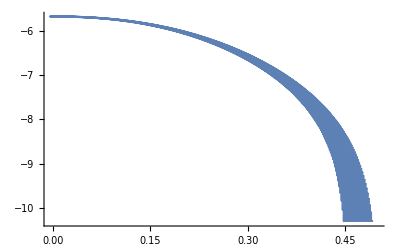

```mathematica
ListLinePlot[Table[{rnsSoln⟦i,3⟧,Log[rnsSoln⟦i,9⟧]},{i,1,Length[rnsSoln]}]]
```

Find analytic derivatives to convert to (x, y, z) coordinates

```mathematica
sr[r_]:=r/(r+rStar);
s[x_,y_,z_]:= Sqrt[x^2+y^2+z^2]/(Sqrt[x^2+y^2+z^2]+rStar);
μ[x_,y_,z_]:=z/Sqrt[x^2+y^2+z^2];
dsdx=Simplify[D[s[x,y,z],x]];
dsdy=Simplify[D[s[x,y,z],y]];
dsdz=Simplify[D[s[x,y,z],z]];
dμdx=Simplify[D[μ[x,y,z],x]];
dμdy=Simplify[D[μ[x,y,z],y]];
dμdz=Simplify[D[μ[x,y,z],z]];
```

Create the interpolating functions and clear the original list data

```mathematica
ρsμ=Interpolation[ rnsSoln⟦;;,{3,4,5}⟧ ];
γsμ=Interpolation[ rnsSoln⟦;;,{3,4,6}⟧ ];
αsμ=Interpolation[ rnsSoln⟦;;,{3,4,7}⟧ ];
ωsμ=Interpolation[ rnsSoln⟦;;,{3,4,8}⟧ ];

esμ=Interpolation[ rnsSoln⟦;;,{3,4,9}⟧ ];
psμ=Interpolation[ rnsSoln⟦;;,{3,4,10}⟧ ];
hsμ=Interpolation[ rnsSoln⟦;;,{3,4,11}⟧ ];
v2sμ=Interpolation[ rnsSoln⟦;;,{3,4,12}⟧ ];

Clear[rnsSoln]
```

We only need the hydro portion of the solution for calculating j^i,the momentum density,
so calculate, then clear the original interpolating functions

```mathematica
baryonmass= 2π rStar^3 NIntegrate[ (( esμ[s,μ] + psμ[s,μ]) ⅇ^(-hsμ[s,μ]))/(√(1-v2sμ[s,μ])) ⅇ^(2 αsμ[s,μ]+(γsμ[s,μ]-ρsμ[s,μ])/2) s^2/(1-s)^4,{s,0,0.8},{μ,0,1},PrecisionGoal-> 5]
```

0.968575

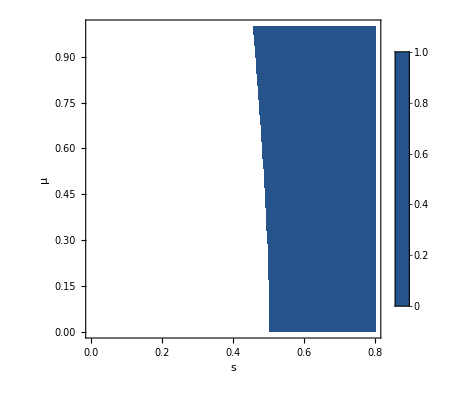

```mathematica
ContourPlot[((Γ-1) esμ[s,μ] - psμ[s,μ])/(√(1-v2sμ[s,μ])) ,{s,0,0.8},{μ,0,1},PlotLegends->Automatic, FrameLabel-> {s,μ}]
```

Derivatives of ω

```mathematica
dωds=D[ωsμ[s,μ],s];
dωdμ=D[ωsμ[s,μ],μ];
Plot[ dωds[s,0],dωdμ[s,0],{s,0,0.5}]
```

Plot::nonopt: Options expected (instead of {s, 0, 0.5}) beyond position 2 in Plot[dωds[s, 0], dωdμ[s, 0], {s, 0, 0.5}]. An option must be a rule or a list of rules.

Plot[dωds[s,0],dωdμ[s,0],{s,0,0.5}]

### Overview of Solution

We only need the hydro portion of the solution for calculating j^i,the momentum density,
so calculate, then clear the original interpolating functions

First, set rules to calculate interesting quantities

```mathematica
jϕ[s_,μ_]:=( (esμ[s,μ]+psμ[s,μ])/(1-v2sμ[s,μ]))Sqrt[v2sμ[s,μ]];
βy[x_]:= -x ωsμ[sr[x],0] ⅇ^((-2 αsμ[sr[x],0]+γsμ[sr[x],0]-ρsμ[sr[x],0])*0.5);
magv[r_]:= Sqrt[v2sμ[sr[r],0]];
lapse[r_]:= ⅇ^((γsμ[sr[r],0]+ρsμ[sr[r],0])*0.5);
doubleαK[x_]:= -2 (D[ωsμ[s,μ[x,0,0]],s] dsdy + D[ωsμ[sr[x],μ],μ] dμdy ) x+2 -(4 dαdy+dσdy) x ω
doubleαK[x_,y_,z_]:=2( (D[ωsμ[s,μ[x,y,z]],s]dsdx ) y-2 dωdy x)+2 +(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω
(* doubleαK[x_,y_,z_]:=2(dωdx y-2 dωdy x)+2 +(-(4 dαdy+dσdy) x+(4 dαdx+dσdx) y) ω *)
(* doubleαK[x_,0,0]:= -2 dωdy x -(4 dαdy+dσdy) x ω *)
```

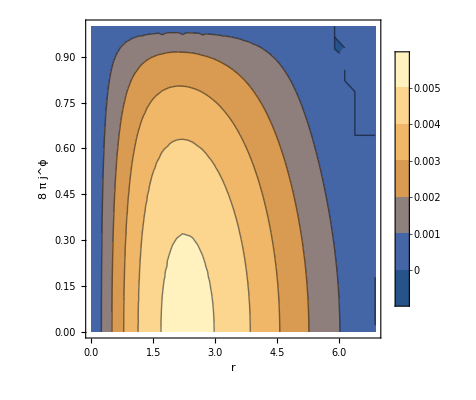

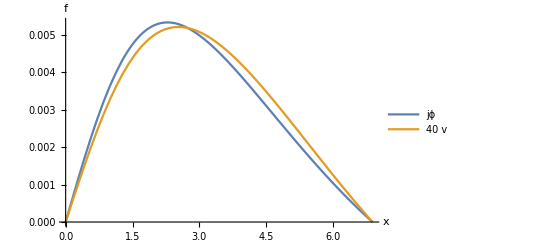

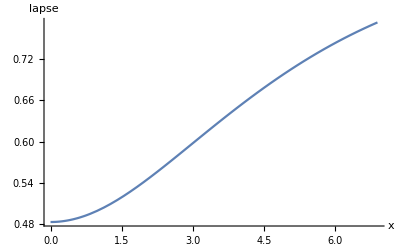

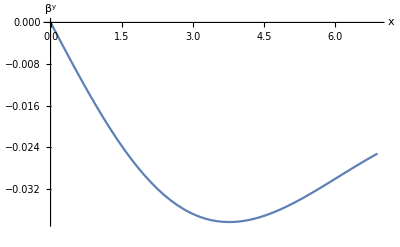

```mathematica
ContourPlot[ 8 π jϕ[sr[r],μ],{r,0,rStar},{μ,0,1},PlotLegends->Automatic, FrameLabel-> {r,8π j^ϕ}]
Plot[ {8 π jϕ[sr[r],0],40*(esμ[sr[r],0]+psμ[sr[r],0])/(1-v2sμ[sr[r],0]) Sqrt[v2sμ[sr[r],0]] ⅇ^(-αsμ[sr[r],0])},{r,0,rStar},
         PlotLegends->{"jϕ","40 v"},AxesLabel-> {x,f}]
Plot[ lapse[r],{r,0,rStar},AxesLabel-> {x,lapse}]
Plot[βy[r],{r,0,rStar},AxesLabel-> {x,β^y}]
```

Create the derivatives of these metric potentials in (s,μ) space

```mathematica
dρds=Derivative[1,0][ρsμ];
dρdμ=Derivative[0,1][ρsμ];
dγds=Derivative[1,0][γsμ];
dγdμ=Derivative[0,1][γsμ];
dαds=Derivative[1,0][αsμ];
dαdμ=Derivative[0,1][αsμ];
dωds=Derivative[1,0][αsμ];
dωdμ=Derivative[0,1][αsμ];

(* dρdx^i *)
dρdx[x_,y_,z_]:= dsdx dρds[ s[x,y,z], μ[x,y,z]] + dμdx dρdμ[ s[x,y,z], μ[x,y,z]];
dρdy[x_,y_,z_]:= dsdy dρds[ s[x,y,z], μ[x,y,z]] + dμdy dρdμ[ s[x,y,z], μ[x,y,z]];
dρdz[x_,y_,z_]:= dsdz dρds[ s[x,y,z], μ[x,y,z]] + dμdz dρdμ[ s[x,y,z], μ[x,y,z]];

(* dγdx^i *)
dγdx[x_,y_,z_]:= dsdx dγds[ s[x,y,z], μ[x,y,z]] + dμdx dγdμ[ s[x,y,z], μ[x,y,z]];
dγdy[x_,y_,z_]:= dsdy dγds[ s[x,y,z], μ[x,y,z]] + dμdy dγdμ[ s[x,y,z], μ[x,y,z]];
dγdz[x_,y_,z_]:= dsdz dγds[ s[x,y,z], μ[x,y,z]] + dμdz dγdμ[ s[x,y,z], μ[x,y,z]];

(* dαdx^i *)
dαdx[x_,y_,z_]:= dsdx dαds[ s[x,y,z], μ[x,y,z]] + dμdx dαdμ[ s[x,y,z], μ[x,y,z]];
dαdy[x_,y_,z_]:= dsdy dαds[ s[x,y,z], μ[x,y,z]] + dμdy dαdμ[ s[x,y,z], μ[x,y,z]];
dαdz[x_,y_,z_]:= dsdz dαds[ s[x,y,z], μ[x,y,z]] + dμdz dαdμ[ s[x,y,z], μ[x,y,z]];

(* dωdx^i *)
dωdx[x_,y_,z_]:= dsdx dωds[ s[x,y,z], μ[x,y,z]] + dμdx dωdμ[ s[x,y,z], μ[x,y,z]];
dωdy[x_,y_,z_]:= dsdy dωds[ s[x,y,z], μ[x,y,z]] + dμdy dωdμ[ s[x,y,z], μ[x,y,z]];
dωdz[x_,y_,z_]:= dsdz dωds[ s[x,y,z], μ[x,y,z]] + dμdz dωdμ[ s[x,y,z], μ[x,y,z]];
```

Create the 2^nd order derivatives for the momentum constraint ...

Copy solution from analytic above if undefined

Create functional dependence of the shift in (x,y,z)

```mathematica
analyticToFcns:={ρ-> ρsμ[s[x,y,z],μ[x,y,z]],α-> αsμ[s[x,y,z],μ[x,y,z]],γ-> γsμ[s[x,y,z],μ[x,y,z]]ω-> ωsμ[s[x,y,z],μ[x,y,z]]};
```

```mathematica
α[x_,y_,z_]:= αsμ[ N[s[x,y,z]], N[μ[x,y,z] ]];
ρ[x_,y_,z_]:= ρsμ[ N[s[x,y,z]], N[μ[x,y,z] ]];
γ[x_,y_,z_]:= γsμ[ N[s[x,y,z]], N[μ[x,y,z] ]];
ω[x_,y_,z_]:= ωsμ[ N[s[x,y,z]], N[μ[x,y,z] ]];
σ[x_,y_,z_]:= γsμ[ N[s[x,y,z]], N[μ[x,y,z] ]]-ρsμ[ N[s[x,y,z]], N[μ[x,y,z] ]];
```

```mathematica
beta3[xv_,yv_,zv_]:=beta3downc/.{x-> xv,y->yv,z->zv}
```

```mathematica
beta3[3,2,5]
```

{0.0145919,-0.0218878,0}

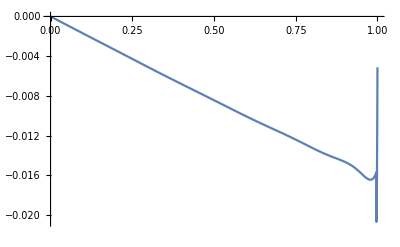

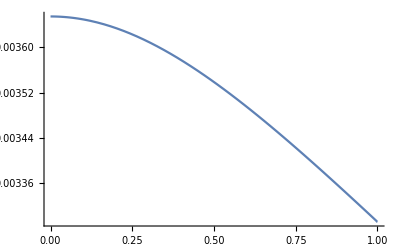

-0.969839

-0.980294

5.63297×10^-6

-0.0084403

```mathematica
Plot[ N[dωdμ[0.3,μ]],{μ,0,1}]
Plot[ N[ωsμ[0.5,μ]],{μ,0,1}]
N[dωds[0.3,0]]
N[dωds[0.3,0.5]]
N[dωdμ[0.3,0]]
N[dωdμ[0.3,0.5]]
```

```mathematica
sL=0.298746; μL=0.500734;
N[dωds[sL,μL]]
N[dωdμ[sL,μL]]
```

-0.98215

-0.00840263

#### Set quantities for checks, General

We must remember that the derivatives of the potentials within Kij are also dependent on space! Define extra rules to make 2nd derivatives of these readable, and use the chain rule.

```mathematica
readablederivs2:=Flatten[ {
   {Derivative[1,1,0][α][x,y,z]-> dαdxdy,Derivative[1,0,0][α][x,y,z]-> dαdx,Derivative[0,0,1][α][x,y,z]-> dαdz},
{Derivative[0,1,0][ω][x,y,z]-> dωdy,Derivative[1,0,0][ω][x,y,z]-> dωdx,Derivative[0,0,1][ω][x,y,z]-> dωdz},
{Derivative[0,1,0][σ][x,y,z]-> dσdy,Derivative[1,0,0][σ][x,y,z]-> dσdx,Derivative[0,0,1][σ][x,y,z]-> dσdz},
{Derivative[0,1,0][ρ][x,y,z]-> dρdy,Derivative[1,0,0][ρ][x,y,z]-> dρdx,Derivative[0,0,1][ρ][x,y,z]-> dρdz},
{Derivative[0,1,0][γ][x,y,z]-> dγdy,Derivative[1,0,0][γ][x,y,z]-> dγdx,Derivative[0,0,1][γ][x,y,z]-> dγdz},
{Derivative[0,1,0][invα][x,y,z]-> -invα^2 dlapsedy,Derivative[1,0,0][invα][x,y,z]-> -invα^2 dlapsedx,Derivative[0,0,1][invα][x,y,z]-> -invα^2 dlapsedz}}];
```

```mathematica
KijminusγijKc=Simplify[ uKijc - uγijc*TraceKc ];
KijminusγijKc⟦1,3⟧/.fullreadable
```

uKijc

```mathematica
DiKjkc=gencoderivUUTens[KijminusγijKc];
```

```mathematica
Simplify[Sum[ DiKjkc⟦i,3,i⟧,{i,1,3}]]/.fullreadable/.toxaxis
```

Part::partw: Part 2 of {{uKijc - TraceKc (Power[« 2 »] Power[« 2 »] + Power[« 2 »] Power[« 2 »])/Power[« 2 »] + Power[« 2 »], uKijc + (ⅇ^Plus[« 2 »] - Power[« 2 »]) TraceKc x y/Power[« 2 »] + Power[« 2 »], uKijc}, {uKijc + (ⅇ^Plus[« 2 »] - Power[« 2 »]) TraceKc x y/Power[« 2 »] + Power[« 2 »], uKijc - TraceKc (Power[« 2 »] Power[« 2 »] + Power[« 2 »] Power[« 2 »])/Power[« 2 »] + Power[« 2 »], uKijc}, {uKijc, uKijc, -ⅇ^-2 TagBox[InterpolatingFunction[« 5 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 2 »] TraceKc + uKijc}} does not exist.

Part::partw: Part 3 of {{uKijc - TraceKc (Power[« 2 »] Power[« 2 »] + Power[« 2 »] Power[« 2 »])/Power[« 2 »] + Power[« 2 »], uKijc + (ⅇ^Plus[« 2 »] - Power[« 2 »]) TraceKc x y/Power[« 2 »] + Power[« 2 »], uKijc}, {uKijc + (ⅇ^Plus[« 2 »] - Power[« 2 »]) TraceKc x y/Power[« 2 »] + Power[« 2 »], uKijc - TraceKc (Power[« 2 »] Power[« 2 »] + Power[« 2 »] Power[« 2 »])/Power[« 2 »] + Power[« 2 »], uKijc}, {uKijc, uKijc, -ⅇ^-2 TagBox[InterpolatingFunction[« 5 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 2 »] TraceKc + uKijc}} does not exist.

Part::partw: Part 2 of gencoderivUUTens[{{uKijc - TraceKc\ (Power[« 2 »]\ Power[« 2 »] + Power[« 2 »]\ Power[« 2 »])/Power[« 2 »] + Power[« 2 »], uKijc + (-Power[« 2 »] + ⅇ^Plus[« 2 »])\ TraceKc\ x\ y/Power[« 2 »] + Power[« 2 »], uKijc}, {uKijc + (-Power[« 2 »] + ⅇ^Plus[« 2 »])\ TraceKc\ x\ y/Power[« 2 »] + Power[« 2 »], uKijc - TraceKc\ (Power[« 2 »]\ Power[« 2 »] + Power[« 2 »]\ Power[« 2 »])/Power[« 2 »] + Power[« 2 »], uKijc}, {uKijc, uKijc, -ⅇ^-2\ α\ TraceKc + uKijc}}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

uKijc+gencoderivUUTens[{{-ⅇ^(-2 α) TraceKc+uKijc,uKijc,uKijc},{uKijc,-ⅇ^(-γ+ρ) TraceKc+uKijc,uKijc},{uKijc,uKijc,-ⅇ^(-2 α) TraceKc+uKijc}}]⟦2,3,2⟧+gencoderivUUTens[{{-ⅇ^(-2 α) TraceKc+uKijc,uKijc,uKijc},{uKijc,-ⅇ^(-γ+ρ) TraceKc+uKijc,uKijc},{uKijc,uKijc,-ⅇ^(-2 α) TraceKc+uKijc}}]⟦3,3,3⟧

```mathematica
KijminusγijKc=FullSimplify[ uKijc - uγijc*TraceKc ];
DiKjkc=gencoderivUUTens[KijminusγijKc];
jic=1/(8 π)TensorContract[ DiKjkc, {1,3} ] ;
```

$Aborted

```mathematica
DiKjk=FullSimplify[ DiKjkc/.fullreadable,dρdγ2dσ];
ji=1/(8 π)TensorContract[ DiKjk, {1,3} ] ;
```

$Aborted